```mathematica
Needs["VisualizeGenome`"]
Needs["BSFHistory`"]
```

```mathematica
convertGPATGenome[{"atan"["gauss"["plus"[0.2534219065387728 x0,4.630118948088606,-3.3017315841480586 x0,3.5686227847827148 x0],1]]}]
```

{ArcTan[ⅇ^(-(5.63012+0.520313 x0)^2)]}

```mathematica
listBSF["~/java/exp/GPAT3D_H_H2_200/run_001_132_GENOMES_MATH.txt"]//MatrixForm
```

(last
68945
68831
{times[times[times[plus[1.49998 times[x2,x0,x1,x1,times[1],1],5.32038,-0.185641 gauss[x1,x2,x2,1,x2],-1.09501 x1,2.30025 times[1,x1,x0,x2]],1],1]]}
0.990983)

```mathematica
(evo1=listBSFEvolution["~/java/exp/GPAT4D_E_200_NOREPEAT/run_001_165_GENOMES_MATH.txt"])//MatrixForm;
```

```mathematica
(evo1=listBSFEvolution["~/java/exp/GP4D_E_200/run_001_185_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 64 | -1 | {plus[x1,sin[x0]]} | 0.261555
2 | 179 | 64 | {plus[gauss[-1.],sin[x0]]} | 0.289132
5 | 453 | 179 | {plus[plus[x0,atan[-1.]],sin[x0]]} | 0.332769
7 | 671 | 524 | {plus[plus[x0,atan[x0]],sin[x0]]} | 0.422013
18 | 1789 | 671 | {plus[plus[atan[times[plus[x0,-2.02099],plus[x1,x2]]],atan[x0]],sin[x0]]} | 0.443176
23 | 2267 | 1789 | {plus[plus[atan[times[plus[x0,-2.02099],plus[x1,x2]]],x0],sin[x0]]} | 0.464294
28 | 2719 | 2698 | {plus[plus[atan[times[plus[x0,-2.02802],plus[x1,x2]]],x0],x0]} | 0.47511
30 | 2921 | 2865 | {plus[plus[atan[times[plus[x0,-2.03641],plus[x2,x2]]],x0],x0]} | 0.534313
33 | 3222 | 2921 | {plus[plus[atan[times[plus[x1,-2.03641],plus[x2,x2]]],x0],x0]} | 0.534313
36 | 3513 | 3434 | {plus[plus[atan[times[plus[1.29575,-2.04561],plus[x2,x2]]],x0],x0]} | 0.57422
59 | 5812 | 5318 | {plus[plus[times[-1.,x2],x0],x0]} | 0.57554
97 | 9657 | 8984 | {plus[plus[times[-1.,x2],x0],times[1.8205,times[x0,gauss[atan[x0]]]]]} | 0.576144
121 | 12099 | 10680 | {plus[plus[times[-1.,x2],x0],times[1.81284,times[x0,gauss[plus[x1,-1.]]]]]} | 0.75382
126 | 12518 | 12431 | {plus[plus[times[-1.,x2],times[x0,2.48538]],times[1.80465,times[x0,gauss[plus[x1,-1.]]]]]} | 0.581787
128 | 12755 | 12518 | {plus[plus[times[-1.,x2],times[x0,2.48538]],times[1.80465,times[x0,atan[x1]]]]} | 0.869525
168 | 16770 | 16351 | {plus[plus[times[atan[-1.77522],x2],times[x0,2.313]],times[1.81051,times[x0,atan[x1]]]]} | 0.885902
257 | 25667 | 25221 | {plus[plus[times[atan[-1.95766],x2],times[x0,2.30277]],times[1.83466,times[x0,atan[times[0.984596,x1]]]]]} | 0.886781
410 | 40911 | 40445 | {plus[plus[times[plus[times[x3,x1],-1.],x2],times[x0,2.30277]],times[2.04003,times[x0,atan[times[0.864505,x1]]]]]} | 0.993268)

```mathematica
showAsExpressions[evo1]/.{x0->Subscript[x, 1],x1->Subscript[x, 2],x2->Subscript[x, 3],x3->Subscript[x, 4]}
```

Gen | Expression | Expanded | f
1 | {Sin[x_1]+x_2} | {Sin[x_1]+x_2} | 0.261555
2 | {0.367879+Sin[x_1]} | {0.367879+Sin[x_1]} | 0.289132
5 | {-0.785398+Sin[x_1]+x_1} | {-0.785398+Sin[x_1]+x_1} | 0.332769
7 | {ArcTan[x_1]+Sin[x_1]+x_1} | {ArcTan[x_1]+Sin[x_1]+x_1} | 0.422013
18 | {ArcTan[x_1]+ArcTan[(-2.02099+x_1) (x_2+x_3)]+Sin[x_1]} | {ArcTan[x_1]+ArcTan[(-2.02099+x_1) (x_2+x_3)]+Sin[x_1]} | 0.443176
23 | {ArcTan[(-2.02099+x_1) (x_2+x_3)]+Sin[x_1]+x_1} | {ArcTan[(-2.02099+x_1) (x_2+x_3)]+Sin[x_1]+x_1} | 0.464294
28 | {ArcTan[(-2.02802+x_1) (x_2+x_3)]+2 x_1} | {ArcTan[(-2.02802+x_1) (x_2+x_3)]+2 x_1} | 0.47511
30 | {ArcTan[2 (-2.03641+x_1) x_3]+2 x_1} | {ArcTan[2 (-2.03641+x_1) x_3]+2 x_1} | 0.534313
33 | {ArcTan[2 (-2.03641+x_2) x_3]+2 x_1} | {ArcTan[2 (-2.03641+x_2) x_3]+2 x_1} | 0.534313
36 | {-ArcTan[1.49971 x_3]+2 x_1} | {-ArcTan[1.49971 x_3]+2 x_1} | 0.57422
59 | {2 x_1-1. x_3} | {2 x_1-1. x_3} | 0.57554
97 | {x_1+1.8205 ⅇ^(-ArcTan[x_1]^2) x_1-1. x_3} | {x_1+1.8205 ⅇ^(-ArcTan[x_1]^2) x_1-1. x_3} | 0.576144
121 | {x_1+1.81284 ⅇ^(-(-1.+x_2)^2) x_1-1. x_3} | {x_1+1.81284 ⅇ^(-(-1.+x_2)^2) x_1-1. x_3} | 0.75382
126 | {2.48538 x_1+1.80465 ⅇ^(-(-1.+x_2)^2) x_1-1. x_3} | {2.48538 x_1+1.80465 ⅇ^(-(-1.+x_2)^2) x_1-1. x_3} | 0.581787
128 | {2.48538 x_1+1.80465 ArcTan[x_2] x_1-1. x_3} | {2.48538 x_1+1.80465 ArcTan[x_2] x_1-1. x_3} | 0.869525
168 | {2.313 x_1+1.81051 ArcTan[x_2] x_1-1.05779 x_3} | {2.313 x_1+1.81051 ArcTan[x_2] x_1-1.05779 x_3} | 0.885902
257 | {2.30277 x_1+1.83466 ArcTan[0.984596 x_2] x_1-1.09853 x_3} | {2.30277 x_1+1.83466 ArcTan[0.984596 x_2] x_1-1.09853 x_3} | 0.886781
410 | {2.30277 x_1+2.04003 ArcTan[0.864505 x_2] x_1+x_3 (-1.+x_2 x_4)} | {2.30277 x_1+2.04003 ArcTan[0.864505 x_2] x_1-1. x_3+x_2 x_3 x_4} | 0.993268

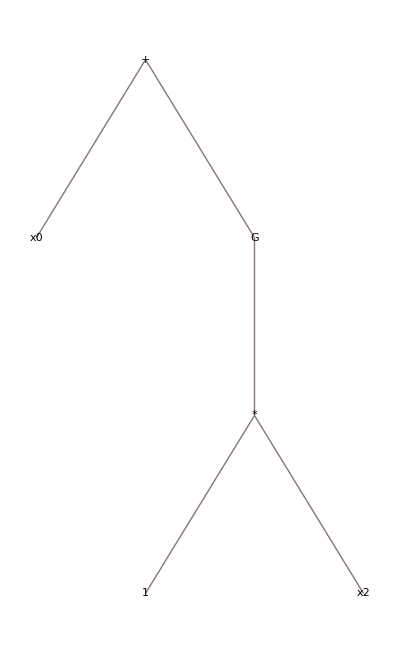
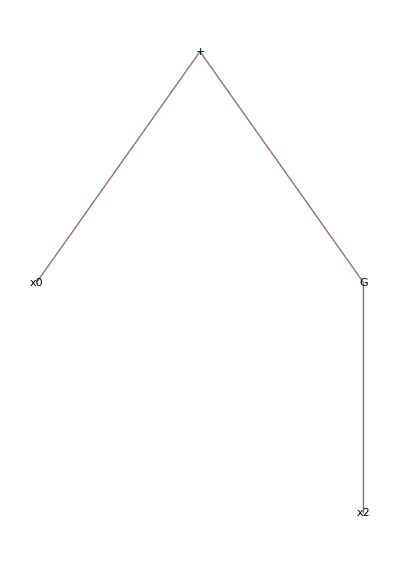
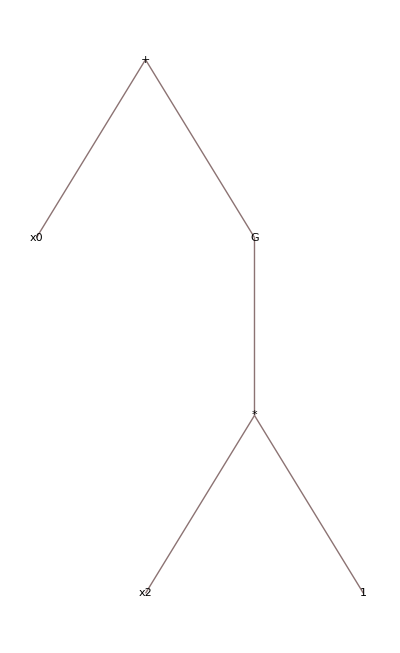
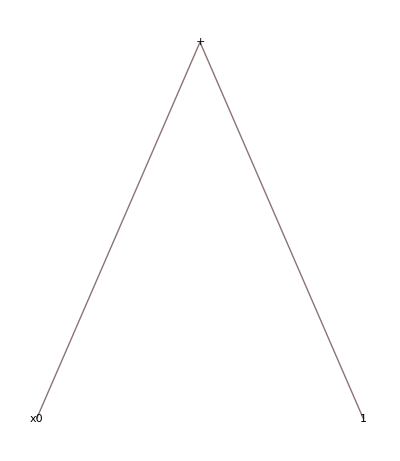
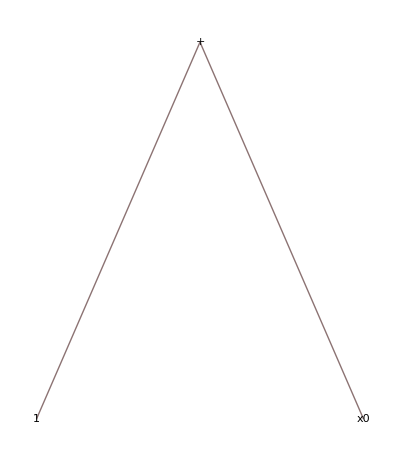
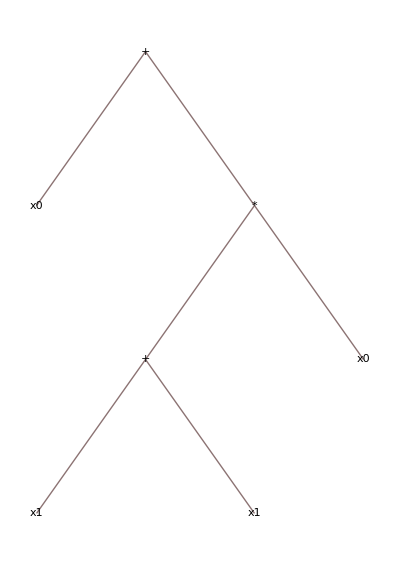
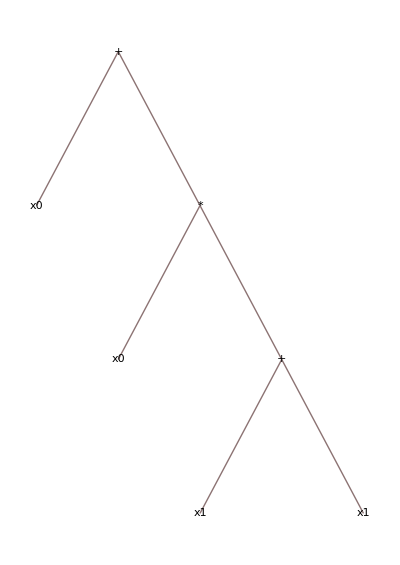
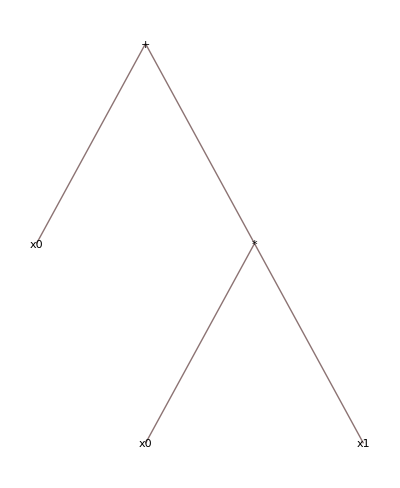
Gen | Genome | Sorted | Simplified | f
1 | -Graphics- | -Graphics- | -Graphics- | 0.281653
3 | -Graphics- | -Graphics- | -Graphics- | 0.299518
4 | -Graphics- | -Graphics- | -Graphics- | 0.241692
5 | -Graphics- | -Graphics- | -Graphics- | 0.379147
9 | -Graphics- | -Graphics- | -Graphics- | 0.326531
10 | -Graphics- | -Graphics- | -Graphics- | 0.492708
11 | -Graphics- | -Graphics- | -Graphics- | 0.461424
13 | -Graphics- | -Graphics- | -Graphics- | 0.44905
15 | -Graphics- | -Graphics- | -Graphics- | 0.492708
18 | -Graphics- | -Graphics- | -Graphics- | 0.554125
32 | -Graphics- | -Graphics- | -Graphics- | 0.573701
55 | -Graphics- | -Graphics- | -Graphics- | 0.855936
77 | -Graphics- | -Graphics- | -Graphics- | 0.884881
149 | -Graphics- | -Graphics- | -Graphics- | 0.995025

```mathematica
showGenomes[evo1]
```

```mathematica
Export["GPAT_H_RUN66.pdf",%]
```

GPAT_H_RUN66.pdf

## 1 D Regression

```mathematica
(evo1=listBSFEvolution["~/java/exp/GPAT1D_G_2/run_001_174_GENOMES_MATH.txt"])//MatrixForm
```

(1 | 17300193 | -1 | {plus} | 2.70569×10^-8
2 | 17300336 | 17300193 | {plus[0.987404]} | 2.70621×10^-8
3 | 17300444 | 17300336 | {plus[0.987404 gauss[1]]} | 2.70588×10^-8
4 | 17300545 | 17300444 | {plus[0.987404 times[1]]} | 2.70621×10^-8
5 | 17300618 | 17300545 | {gauss[plus[0.987404 gauss[1],1.]]} | 2.70577×10^-8
7 | 17300852 | 17300767 | {gauss[plus[0.987404 gauss[1],0.549582,1.3494 x0]]} | 2.70569×10^-8
11 | 17301246 | 17301143 | {gauss[plus[1.82938 gauss[1],-0.878784,4.25122 x0],1]} | 2.70569×10^-8
12 | 17301371 | 17301246 | {times[plus[1.21817 gauss[1],-0.878784,4.24779 x0],1]} | 2.70898×10^-8
14 | 17301559 | 17301465 | {times[plus[1.25431 times[1],-0.865015,4.26333 x0],1]} | 2.70943×10^-8
18 | 17301970 | 17301829 | {times[plus[1.25431 times[1],0.0519364,4.26333 x0],1,x0]} | 2.89265×10^-8
19 | 17302043 | 17301970 | {times[plus[1.25431 times[1,x0],0.052181,4.26333 x0],1,x0]} | 2.94957×10^-8
20 | 17302151 | 17302043 | {times[plus[1.25431 times[1,x0,x0],-0.837428,3.78246 x0],x0,x0]} | 7.4362×10^-7
21 | 17302253 | 17302151 | {times[plus[1.25431 times[1,x0,x0],-0.837428,3.78246 x0],x0,x0,1]} | 7.4362×10^-7
131 | 17313195 | 17313076 | {times[times[plus[1.49973 times[1,x0,x0],-1.14579,2.34657 x0],x0,x0,1]]} | 0.0110484
192 | 17319347 | 17319239 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.15417,2.347 x0],x0,x0,1]]]} | 0.0111279
202 | 17320363 | 17320266 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.15417,2.347 x0],x0,x0,1]],1. x0]} | 0.0120525
362 | 17336319 | 17336198 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.13829,2.32155 x0],x0,x0,1],1],2.1781 x0]} | 0.0388955
428 | 17342956 | 17342831 | {plus[1. times[times[plus[1.49986 times[1,x0,x0],-1.15575,2.29732 x0],x0,x0,1],1],3.93559 x0,1.00118]} | 0.0620225
977 | 17397784 | 17397676 | {plus[1.00023 times[times[plus[1.49986 times[1,x0,x0],-1.11949,2.29902 x0],x0,x0,1],1],3.72859 x0,-4.18753]} | 0.956232)

```mathematica
targetG=1.5*x0^4+2.3*x0^3-1.1*x0^2+3.7*x0-4.5
```

-4.5+3.7 x0-1.1 x0^2+2.3 x0^3+1.5 x0^4

```mathematica
fitness[target_,evolved_]:=
(1/(1+Mean[Table[(target-evolved)^2,{x0,-10,10,20/19}]]))
```

```mathematica
Grid[{Simplify[convertGPATGenome[#][[1]]],
fitness[targetG,convertGPATGenome[#][[1]]]}&/@evo1[[All,4]]]
```

0 | 2.70569×10^-8
0.987404 | 2.70621×10^-8
0.363246 | 2.70588×10^-8
0.987404 | 2.70621×10^-8
0.155916 | 2.70577×10^-8
ⅇ^(-1. (0.912827+1.3494 x0)^2) | 2.70569×10^-8
ⅇ^(-1. (0.794206+4.25122 x0)^2) | 2.70569×10^-8
-0.430645+4.24779 x0 | 2.70898×10^-8
0.38929+4.26333 x0 | 2.70943×10^-8
x0 (1.30624+4.26333 x0) | 2.89265×10^-8
x0 (0.052181+5.51763 x0) | 2.94957×10^-8
x0^2 (-0.837428+3.78246 x0+1.25431 x0^2) | 7.4362×10^-7
x0^2 (-0.837428+3.78246 x0+1.25431 x0^2) | 7.4362×10^-7
x0^2 (-1.14579+2.34657 x0+1.49973 x0^2) | 0.0110484
1. x0^2 (-1.15417+2.347 x0+1.49986 x0^2) | 0.0111279
x0 (1.-1.15417 x0+2.347 x0^2+1.49986 x0^3) | 0.0120525
x0 (2.1781-1.13829 x0+2.32155 x0^2+1.49986 x0^3) | 0.0388955
1.00118+3.93559 x0-1.15575 x0^2+2.29732 x0^3+1.49986 x0^4 | 0.0620225
-4.18753+3.72859 x0-1.11974 x0^2+2.29954 x0^3+1.5002 x0^4 | 0.956232

```mathematica
Manipulate[{fitness[targetG,convertGPATGenome[evo1[[i,4]]][[1]]],Plot[{targetG,convertGPATGenome[evo1[[i,4]]][[1]]},{x0,-10,10},PlotRange->{-150,150},PlotStyle->Thick]},{i,1,Length[evo1],1}]
```